```mathematica
NS["plinkinetti_graphs12"]
```

```mathematica
logt[x_,a_:1]=Sign[x]*Log[10,1+Abs[x/a]];
ilogt[x_,a_:1]=Sign[x]*(10^(Abs[x/a])-1);
logistic=LogisticSigmoid;
semilogistic[x_]=1-Exp[-x];
logit[x_]=Log[x/(1-x)];
xlogy[x_,y_]:=If[x>0,x*Log[x/y],0];
```

```mathematica
km[p1_,p2_]:=Total[Abs[Accumulate[p1-p2]]];
jsd[p1_,p2_]:=Total[MapThread[xlogy,{p1,(p1+p2)/2}]+MapThread[xlogy,{p2,(p1+p2)/2}]]/2;
```

```mathematica
face=Image[Import["face2.png"],ImageSize->20];
robot2=Image[Import["robot2.png"],ImageSize->20,ImageResolution->400];
```

```mathematica
wdo="C:\\Users\\pglpm\\repositories\\plinkinetti\\comparisons11\\";
wd="C:\\Users\\pglpm\\repositories\\plinkinetti\\comparisons12\\";
label="meankm2hga";
parts=Join[Range[1,15],Range[17,37]];
<<"robotdistribution.m";<<"robotdistribution2.m"
```

```mathematica
ClearAll[obs,pdists,rdistso,paramso,rdists,paramsa,params,rdistsom,rdistsm];obs=Import["observation_seqs.csv"];pdists[i_]:=pdists[i]=Import[wdo<>"pdistr"<>ToString[i]<>"_"<>label<>".csv"];
rdistso[i_]:=rdistso[i]=Import[wdo<>"rdistr"<>ToString[i]<>"_"<>label<>".csv"];
paramso=Import[wdo<>"points_meankm2hga.csv"];
paramso=Insert[paramso,{16,Null,Null,Null,Null},16];
rdists[i_]:=rdists[i]=Import[wd<>"rdistr_p"<>ToString[i]<>".csv"];
paramsa[i_]:=paramsa[i]=Import[wd<>"params_p"<>ToString[i]<>".csv"];
params[i_]:=params[i]=paramsa[i][[Ordering[paramsa[i],1,(Norm[#1[[2;;]],1]<Norm[#2[[2;;]],1]&)]]][[1]];
rdistsom[i_]:=rdistsom[i]=robotdistributiono[pdists[i][[1]],paramso[[i,2;;]],obs[[i,2;;201]]];
rdistsm[i_]:=rdistsm[i]=robotdistribution[pdists[i][[1]],params[i],obs[[i,2;;201]]];
```

```mathematica
strangep={};
Do[If[Dimensions[paramsa[i]][[1]]>1,strangep=Append[strangep,{i,paramsa[i]//MF,MF@Table[{Norm[paramsa[i][[j,2;;]]],Norm[paramsa[i][[j,2;;]],1]},{j,Length[paramsa[i]]}]}]],{i,parts}];strangep[[;;,1]]
```

{18,19,29,33,37}

```mathematica
mean[distr_]:=distr.Range[1,40];
std[distr_]:=Sqrt[(distr.(Range[1,40]^2))-(mean[distr]^2)];
```

```mathematica
myfontsize=15;
```

```mathematica
Dimensions[mean@rdistsm[1]]
```

{201}

```mathematica
i=2;ListPlot[{T[{Range[0,200],mean@pdists[i]}],T[{Range[0,200],mean@rdistso[i]}],T[{Range[0,200],mean@rdistsom[i]}]},Joined->{True,True,True,True},PlotMarkers->None,PlotRange->{{0,20},All},PlotStyle->{{grey,Thick},{red,Thin,Opacity[0.75]},{purpleblue,Thin,Dashed,Opacity[0.75]},{green,Thin,DotDashed,Opacity[0.75]}},Axes->None,Frame->{True,True,False,False},Evaluate@myframestyle[15],
FrameLabel->myaxes[{"observation","mean"}],
PlotLabel->mystyle["participant "<>ToString[i]],
PlotLegends->mylegends[{"s.old","m.old","s.new","m.new"},{0.5,1}],AspectRatio->1/2,ImageSize->{a4shortside,a4shortside/2}]
```

-Graphics-

```mathematica
ListPlot[{T[{Range[0,200],std@rdistso[i]}],T[{Range[0,200],std@rdistsom[i]}],T[{Range[0,200],std@rdists[i]}],T[{Range[0,200],std@rdistsm[i]}]},Joined->{True,True,True,True},PlotMarkers->None,PlotRange->{All,All},PlotStyle->{{grey,Thick},{red,Thin,Opacity[0.75]},{purpleblue,Thin,Dashed,Opacity[0.75]},{green,Thin,DotDashed,Opacity[0.75]}},Axes->None,Frame->{True,True,False,False},Evaluate@myframestyle[15],
FrameLabel->myaxes[{"observation","std"}],
PlotLabel->mystyle["participant "<>ToString[i]],
PlotLegends->mylegends[{"s.old","m.old","s.new","m.new"},{0.5,1}],AspectRatio->1/2,ImageSize->{a4shortside,a4shortside/2}]
```

-Graphics-

```mathematica
ListPlot[{T[{Range[0,200],std@rdists[i]}],T[{Range[0,200],std@dist1}]},Joined->{True,True,True},PlotRange->{0,15},PlotStyle->{{red,Thick,Opacity[0.75]},{purpleblue,Thick,Dashed,Opacity[0.75]}},Axes->None,Frame->{True,True,False,False},Evaluate@myframestyle[15],
FrameLabel->myaxes[{"observation","std"}],
PlotLabel->mystyle["participant "<>ToString[i]],
PlotLegends->mylegends[{face,robot2},{0.5,1}],AspectRatio->1/2,ImageSize->{a4shortside,a4shortside/2}]
```

-Graphics-

```mathematica
myfontsize=15;Do[plot=ListPlot[{T[{Range[0,200],mean@rdistsm[i]}],T[{Range[0,200],mean@rdists[i]}]},Joined->{True,True,True},PlotMarkers->{"",""},PlotRange->{1,40},PlotStyle->{{red,Thick,Opacity[0.75]},{purpleblue,Thick,Dashed,Opacity[0.75]}},Axes->None,Frame->{True,True,False,False},Evaluate@myframestyle[15],
FrameLabel->myaxes[{"observation","mean"}],
PlotLabel->mystyle["participant "<>ToString[i]],
PlotLegends->mylegends[{"math","saved"},{0.5,1}],AspectRatio->1/2,ImageSize->{a4shortside,a4shortside/2}];

expdf0[wd<>"justtest"<>ToString[i],plot],
{i,parts}]
```

```mathematica
(* Plot means *)
```

```mathematica
myfontsize=15;Do[plot=ListPlot[{T[{Range[1,200],obs[[i,2;;]]}],T[{Range[0,200],mean@pdists[i]}],T[{Range[0,200],mean@rdistsm[i]}]},Joined->{True,True,True},PlotMarkers->{{Graphics[{Disk[{0,0},0.01]}],0.02},"",""},PlotRange->{1,40},PlotStyle->{{grey,Thin},{red,Thick,Opacity[0.75]},{purpleblue,Thick,Dashed,Opacity[0.75]}},Axes->None,Frame->{True,True,False,False},Evaluate@myframestyle[15],
FrameLabel->myaxes[{"observation","mean"}],
PlotLabel->mystyle["participant "<>ToString[i]],
PlotLegends->mylegends[{"outcome",face,robot2},{0.5,1}],AspectRatio->1/2,ImageSize->{a4shortside,a4shortside/2}];

expdf0[wd<>"means_p"<>ToString[i],plot],
{i,parts}]
```

```mathematica
maxstd=Max@Flatten@Table[{std@pdists[i],std@rdistsm[i]},{i,parts}];
minstd=Min@Flatten@Table[{std@pdists[i],std@rdistsm[i]},{i,parts}];
```

```mathematica
(* Plot stds *)
```

```mathematica
Do[plot=ListPlot[{T[{Range[0,200],std@pdists[i]}],T[{Range[0,200],std@rdistsm[i]}]},Joined->{True,True,True},PlotRange->{minstd,maxstd},PlotStyle->{{red,Thick,Opacity[0.75]},{purpleblue,Thick,Dashed,Opacity[0.75]}},Axes->None,Frame->{True,True,False,False},Evaluate@myframestyle[15],
FrameLabel->myaxes[{"observation","std"}],
PlotLabel->mystyle["participant "<>ToString[i]],
PlotLegends->mylegends[{face,robot2},{0.5,1}],AspectRatio->1/2,ImageSize->{a4shortside,a4shortside/2}];

expdf0[wd<>"std_p"<>ToString[i],plot],
{i,parts}]
```

```mathematica
ClearAll[jst,kmt];jst[i_]:=Table[jsd[pdists[i][[j]],rdistsm[i][[j]]],{j,201}];
kmt[i_]:=Table[km[pdists[i][[j]],rdistsm[i][[j]]],{j,201}];
```

```mathematica
maxjst=Max@Flatten@Table[jst[i],{i,parts}];maxkmt=Max@Flatten@Table[kmt[i],{i,parts}];
```

```mathematica
(* Plot discrepancies *)
```

```mathematica
imgpad={{45,50},{45,10}};Do[plot1=ListPlot[T[{Range[0,200],kmt[i]}],Joined->True,PlotRange->{0,maxkmt},PlotStyle->{green,Thick,Opacity[0.75]},Axes->None,Frame->{True,True,False,False},FrameStyle->{Directive[Black,myfontsize,Thickness[1/500],FontFamily->Auto],Directive[green,myfontsize,Thickness[1/500],FontFamily->Auto],Auto,Auto},
FrameTicks->All,
FrameLabel->{Style["observation",Black,myfontsize,Thickness[1/50],FontFamily->Auto],Style["K distance",green,myfontsize,Thickness[1/50],FontFamily->Auto]},
PlotLabel->mystyle["participant "<>ToString[i]],
PlotLegends->mylegends[{"K distance"},{0.25,1}],AspectRatio->1/2,ImageSize->{a4shortside,a4shortside/1.7},ImagePadding->imgpad];

plot2=ListPlot[T[{Range[0,200],jst[i]}],Joined->True,PlotRange->{0,maxjst},PlotStyle->{yellow,Thick,Dashed,Opacity[0.75]},Axes->None,Frame->{False,False,False,True},
FrameTicks->All,FrameStyle->{Auto,Auto,Auto,Directive[yellow,myfontsize,Thickness[1/500],FontFamily->Auto]},
FrameLabel->{{None,Style["JS distance",yellow,myfontsize,Thickness[1/50],FontFamily->Auto]},{None,None}},
PlotLabel->mystyle[""],
PlotLegends->mylegends[{"JS distance"},{0.75,1}],AspectRatio->1/2,ImageSize->{a4shortside,a4shortside/1.7},ImagePadding->imgpad];

expdf0[wd<>"discr_p"<>ToString[i],Overlay[{plot1,plot2}]]
,{i,parts}]
```

```mathematica
cpl[s_,m_,p_]:=p.{1,m,s};cp[s_,m_,p_]:=LogisticSigmoid[cpl[s,m,p]];
```

```mathematica
cpi[i_]:=cpi[i]=Table[{m,s,cp[s,m,params[[i,3;;5]]]},{s,0,m-1},{m,1,199}]
```

```mathematica
(* Plot changepoint function *)
```

```mathematica
i=12;DensityPlot[cp[s,m,params[i][[2;;]]],{m,2,200},{s,1,199},PlotRange->{{0,201},{-1,201},{0,1}},RegionFunction->Function[{x,y},2≤x≤200&&1≤y≤x-1],BoundaryStyle->red,Frame->{{False,True},{True,False}},ColorFunction->(GrayLevel[1-#]&),ColorFunctionScaling->False,PlotRangeClipping->False,PlotPoints->100,FrameTicks->All,
PlotLabel->mystyle["changepoint function participant "<>ToString[i]],PlotLegends->Placed[All,Left],AspectRatio->1/2,FrameLabel->{{None,Style[v,Black,myfontsize,Thickness[1/50],FontFamily->Auto]},{Style[m,Black,myfontsize,Thickness[1/50],FontFamily->Auto],None}},Epilog->Text[mystyle[Style[Λ,Italic] ==Exp@ params[i][[1]]],Scaled[{0.1,0.9}],{-1,0}]]
```

-Graphics-

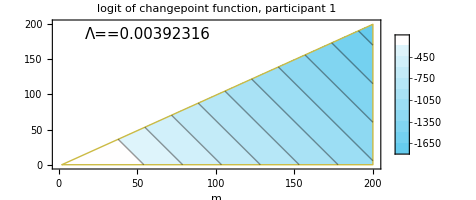

```mathematica
minh=Minimize[{cpl[s,m,tpar[[1,2;;]]],2≤m≤200,1≤s≤ m-1},{s,m}][[1]];
maxh=Maximize[{cpl[s,m,tpar[[1,2;;]]],2≤m≤200,1≤s≤ m-1},{s,m}][[1]];

suph=Max@Abs@{maxh,minh};

plot=ContourPlot[cpl[s,m,tpar[[1,2;;]]],{m,2,200},{s,1,199},PlotRange->{{0,201},{-1,201},All},RegionFunction->Function[{x,y},2≤x≤200&&1≤y≤x-1],BoundaryStyle->yellow,Frame->{{False,True},{True,False}},ColorFunction->(mycolorfunction[#,suph]&),ColorFunctionScaling->False,PlotRangeClipping->False,PlotPoints->100,Contours->10,FrameTicks->All,
PlotLabel->mystyle["logit of changepoint function, participant "<>ToString[i]],PlotLegends->Placed[All,Left],AspectRatio->1/2,FrameLabel->{{None,Style[v,Black,myfontsize,Thickness[1/50],FontFamily->Auto]},{Style[m,Black,myfontsize,Thickness[1/50],FontFamily->Auto],None}},Epilog->Text[mystyle[Style[Λ,Italic] ==Exp@ params[[i,2]]],Scaled[{0.1,0.9}],{-1,0}]]
```

```mathematica
Do[minh=Minimize[{cpl[s,m,tpar[[1,2;;]]],2≤m≤200,1≤s≤ m-1},{s,m}][[1]];
maxh=Maximize[{cpl[s,m,tpar[[1,2;;]]],2≤m≤200,1≤s≤ m-1},{s,m}][[1]];

suph=Max@Abs@{maxh,minh};

plot=ContourPlot[cpl[s,m,tpar[[1,2;;]]],{m,2,200},{s,1,199},PlotRange->{{0,201},{-1,201},All},RegionFunction->Function[{x,y},2≤x≤200&&1≤y≤x-1],BoundaryStyle->yellow,Frame->{{False,True},{True,False}},ColorFunction->(mycolorfunction[#,suph]&),ColorFunctionScaling->False,PlotRangeClipping->False,PlotPoints->100,Contours->10,FrameTicks->All,
PlotLabel->mystyle["logit of changepoint function, participant "<>ToString[i]],PlotLegends->Placed[All,Left],AspectRatio->1/2,FrameLabel->{{None,Style[v,Black,myfontsize,Thickness[1/50],FontFamily->Auto]},{Style[m,Black,myfontsize,Thickness[1/50],FontFamily->Auto],None}},Epilog->Text[mystyle[Style[Λ,Italic] ==Exp@ params[[i,2]]],Scaled[{0.1,0.9}],{-1,0}]];
expng["graph_km\\logitchangep_p"<>ToString[i]<>"_km",plot]
,{i,parts}]
```

```mathematica
<<"avgcp.m";Do[plot=DensityPlot[cp[s,m,params[i][[2;;]]],{m,2,200},{s,1,199},PlotRange->{{0,201},{-1,201},{0,1}},RegionFunction->Function[{x,y},2≤x≤200&&1≤y≤x-1],BoundaryStyle->red,Frame->{{False,True},{True,False}},ColorFunction->(GrayLevel[1-#]&),ColorFunctionScaling->False,PlotRangeClipping->False,PlotPoints->100,FrameTicks->All,
PlotLabel->mystyle["changepoint-function participant "<>ToString[i]],PlotLegends->Placed[All,Left],AspectRatio->1/2,FrameLabel->{{None,Style[v,Black,myfontsize,Thickness[1/50],FontFamily->Auto]},{Style[m,Black,myfontsize,Thickness[1/50],FontFamily->Auto],None}},Epilog->Text[mystyle[ToString@Style[Λ,Italic] <>" = "<>ToString@Exp@ params[i][[1]]<>",   average = "<>ToString@avgcp[200, params[i][[2;;]]],18],Scaled[{0.1,0.9}],{-1,0}]];
expng[wd<>"changep_p"<>ToString[i],plot]
,{i,{1}}]
```

```mathematica
allcpfs=Table[DensityPlot[cp[s-1,m-1,params[[i,3;;5]]],{m,2,200},{s,1,199},PlotRange->{{0,201},{-1,201},{0,1}},RegionFunction->Function[{x,y},2≤x≤200&&1≤y≤x-1],BoundaryStyle->red,Frame->{{False,True},{True,False}},ColorFunction->(GrayLevel[1-#]&),ColorFunctionScaling->False,PlotRangeClipping->False,PlotPoints->100,FrameTicks->All,
PlotLabel->mystyle["participant "<>ToString[i]],PlotLegends->Placed[All,Left],AspectRatio->1/2,FrameLabel->{{None,Style[v,Black,myfontsize,Thickness[1/50],FontFamily->Auto]},{Style[m,Black,myfontsize,Thickness[1/50],FontFamily->Auto],None}},Epilog->Text[mystyle[Style[Λ,Italic] ==Exp@ params[[i,2]]],Scaled[{0.1,0.9}],{-1,0}]],{i,parts}];
```

```mathematica
Export["allcpfs.pdf",Grid[ArrayReshape[allcpfs,{8,5}],Spacings->{0,0}]];
```

```mathematica
expng["testme"]
```

testme.png

```mathematica
n=L
```

```mathematica
n=Length[obs[[6]]]-1;
cumf=Table[0,{n},{40}];
Do[cumf[[i,obs[[6,i+1]]]]=1,{i,n}];
cumf=Accumulate[cumf];
```

```mathematica
Do[plot=ListPlot[{T[{Range[1,200],obs[[1,2;;]]}],T[{Range[0,200],mean@pdists[i]}],T[{Range[0,200],mean@rdists[i]}]},Joined->{True,True,True},PlotMarkers->{{Graphics[{Disk[{0,0},0.01]}],0.02},"",""},PlotRange->{1,40},PlotStyle->{{grey,Thin},{red,Thick,Opacity[0.75]},{purpleblue,Thick,Dashed,Opacity[0.75]}},Axes->None,Frame->{True,True,False,False},Evaluate@myframestyle[15],
FrameLabel->myaxes[{"observation","mean"}],
PlotLabel->mystyle["participant "<>ToString[i]],
PlotLegends->mylegends[{"outcome",face,robot2},{0.5,1}],AspectRatio->1/2,ImageSize->{a4shortside,a4shortside/2}];

expdf0["means_p"<>ToString[i]<>"_km",plot],
{i,parts}]
```

```mathematica
expdf0["testrl"]
```

testrl.pdf

```mathematica
Do[jst=Table[jsd[pdists[i][[j]],rdists[i][[j]]],{j,201}];
kmt=Table[km[pdists[i][[j]],rdists[i][[j]]],{j,201}];

plot=ListPlot[{T[{Range[0,200],kmt}],T[{Range[0,200],jst}]},Joined->{True,True,True},PlotRange->{minstd,maxstd},PlotStyle->{{green,Thick,Opacity[0.75]},{yellow,Thick,Dashed,Opacity[0.75]}},Axes->None,Frame->{True,True,False,False},Evaluate@myframestyle[15],
FrameLabel->myaxes[{"observation","std"}],
PlotLabel->mystyle["participant "<>ToString[i]],
PlotLegends->mylegends[{face,robot2},{0.5,1}],AspectRatio->1/2,ImageSize->{a4shortside,a4shortside/2}];

expdf0["std_p"<>ToString[i]<>"_km",plot],
{i,parts}]
```

```mathematica
jsds=Table[
Mean@Table[jsd[pdists[i][[j]],rdists[i][[j]]],{j,201}]
,{i,parts}]
```

{0.0993772,0.00364069,0.148928,0.0569079,0.261384,0.0390831,0.251955,0.0905575,0.0416622,0.134381,0.0389707,0.0493197,0.0921684,0.00683605,0.270714,0.00534013,0.00371694,0.0682766,0.0852479,0.0587686,0.0782703,0.0650108,0.0445418,0.048148,0.0139286,0.0630536,0.0718753,0.0557745,0.0732668,0.1051,0.0744426,0.294216,0.0575291,0.121505,0.161204,0.071989,0.141243,0.121521,0.230279}

```mathematica
Through[{Mean,Std,Quantile[#,1/4]&,Quantile[#,3/4]&,Max}[jsds]]
```

{0.0948753,0.0750031,0.048148,0.121521,0.294216}

```mathematica
kms=Table[
Mean[Table[km[pdists[i][[j]],rdists[i][[j]]],{j,201}]^2]
,{i,parts}]
```

{2.61276,0.0894319,9.63938,1.36529,5.85108,3.39938,12.2772,2.12124,2.33435,1.99767,1.92105,1.88026,5.08389,0.582363,7.40793,0.46411,0.343312,2.34322,7.65474,1.1845,2.65684,1.54865,0.920667,0.583014,0.730777,1.91472,3.63718,0.684,8.82315,10.6941,2.91042,18.9769,0.69848,2.75067,2.41051,1.4302,2.66746,3.11275,4.8803}

```mathematica
Through[{Mean,Std,Quantile[#,1/4]&,Quantile[#,3/4]&,Max}[kms]]
```

{3.656,3.89207,1.1845,4.8803,18.9769}

```mathematica
wd="C:\\Users\\pglpm\\repositories\\plinkinetti\\comparisons7c\\";
label="mean1jsd";
parts=Join[Range[1,15],Range[17,40]];
```

```mathematica
Do[pdists[i]=Import[wd<>"pdistr"<>ToString[i]<>"_"<>label<>".csv"];
rdists[i]=Import[wd<>"rdistr"<>ToString[i]<>"_"<>label<>".csv"];
,{i,parts}]
```

```mathematica
jsds=Table[
Mean@Table[jsd[pdists[i][[j]],rdists[i][[j]]],{j,201}]
,{i,parts}]
```

{0.0765796,0.00355378,0.135515,0.0552162,0.14369,0.034513,0.183412,0.0183988,0.0392441,0.105663,0.0308545,0.0451551,0.0904422,0.00533001,0.173889,0.00478623,0.00364021,0.0546038,0.0624696,0.0640398,0.0788823,0.0648099,0.0337751,0.0479645,0.00849954,0.0624737,0.0596919,0.0520734,0.0399005,0.10093,0.0734605,0.0732725,0.0573807,0.0997069,0.134951,0.0719141,0.132379,0.121005,0.207985}

```mathematica
Through[{Mean,Std,Quantile[#,1/4]&,Quantile[#,3/4]&,Max}[jsds]]
```

{0.0731295,0.0502303,0.0392441,0.10093,0.207985}

```mathematica
kms=Table[
Mean[Table[km[pdists[i][[j]],rdists[i][[j]]],{j,201}]^2]
,{i,parts}]
```

{5.06443,0.126556,14.2716,2.13163,11.7793,4.64877,17.3631,4.83972,3.09642,4.72131,2.83446,1.78999,5.37131,0.70554,10.9121,0.747784,0.589372,5.51525,11.9982,1.44782,2.87916,1.58501,0.697489,1.6505,1.62409,2.55814,3.88064,0.86981,17.7739,11.6176,3.61975,2.44471,0.706656,3.26717,3.28327,1.43893,3.08307,3.82769,11.6331}

```mathematica
Through[{Mean,Std,Quantile[#,1/4]&,Quantile[#,3/4]&,Max}[kms]]
```

{4.83065,4.72439,1.58501,5.37131,17.7739}